```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
```

```mathematica
PlottingElectionElectorsPie["camera"]
```

-Graphics-

```mathematica
PlottingElectionVotersPie["camera", query->"ELETTORI = 13746"]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie["camera"]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars["camera"]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
luigidimaio=PlottingCandidate["luigi", "di maio",city->"pomigliano d'arco"]
```

{03 - ACERRA,,,}

```mathematica
notfound = PlottingCandidate["tommaso","azzalin"]
```

{NOT FOUND,,,}

```mathematica
"CAMERA" === ToUpperCase["camera"]
```

True

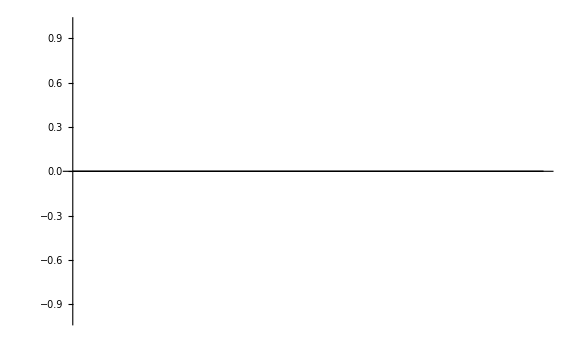

```mathematica
BarChart[notfound[[4]],ChartLegends->notfound[[2]],ImageSize->Large,ChartStyle->"DarkRainbow"]
```

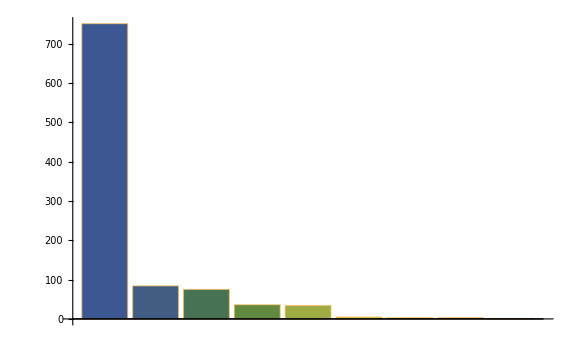

```mathematica
BarChart[luigidimaio[[4]],ChartLegends->luigidimaio[[2]],ImageSize->Large,ChartStyle->"DarkRainbow"]
```

```mathematica
label = "Ciao";

PieChart[{1, 2, 3}, ChartLabels->{label, label, label}]
```

-Graphics-